```mathematica
dir="D:\\betterEnergy"
```

D:\betterEnergy

```mathematica
cell=0;
GetAltitude[frameNo_]:=Module[{path,file,headings,items,applyHeading,organisms},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
Cases[{"pt","y"}/.items,{cell,y_}->y]
]
```

```mathematica
GetAltitude[10000]
```

{10.8034,82.3934,80.3394,97.7531,0.,100.,89.6367,93.8675,98.396,89.9892,75.0962,1.04155,95.5783,99.9947,1.11622,99.9917,99.994,94.4984,2.31755,2.76404,21736,97.0822,97.0823,87.4393,87.4393,87.4393,87.4393,87.4393,87.4393,87.4393,87.4393,87.4393,99.6215,99.6215,99.6215,99.6215,99.6215,99.6215,99.6215,99.6215,99.6215}
 |  |  |  |

```mathematica
fMin=10;
fMax=1040000;
df=10000;
yMax=100;
dy=1;
frames=Table[frame,{frame,fMin,fMax,df}];
data=ParallelMap[BinCounts[GetAltitude[#],{0,yMax,dy}]&,frames];
```

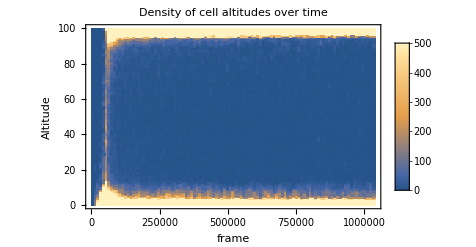

```mathematica
ListDensityPlot[
data//Transpose,
DataRange->{{fMin,fMax},{0,yMax}},
FrameLabel->{"frame","Altitude"},
ClippingStyle->Automatic,
PlotRange->500,
PlotLegends->Placed[Automatic,Right],
InterpolationOrder->0,
AspectRatio->1/GoldenRatio,
PlotLabel->"Density of cell altitudes over time"
]
```

```mathematica
BinCounts[GetAltitude[fMax]]
```

{1,0,0,2,3,2,0,1,0,0,0,0,0,0,0,1,2,0,0,1,1,5,0,0,0,0,2,3,3,1,8,14,26,37,203,464,688,891,10162,9234,2499}

```mathematica
ListPlot3D[
data//Transpose,
DataRange->{{fMin,fMax},{0,yMax}},
AxesLabel->{"frame","Altitude","Density of cell altitudes"},
PlotRange->Full,
BoxRatios->{4,1,1},
ColorFunction->"DarkRainbow"]
```

-Graphics3D-